The moon has been opened up, and land can be obtained for free, but there is a catch. You have to build a wall around the land that you stake out, and building a wall on the moon is expensive. Every country has been allotted a 500 m by 500 m square area, but they will possess only that area which they wall in. 251001 posts have been placed in a rectangular grid with 1 meter spacing. The wall must be a closed series of straight lines, each line running from post to post.

The bigger countries of course have built a 2000 m wall enclosing the entire 250 000 m^2 area. The Duchy of Grand Fenwick, has a tighter budget, and has asked you (their Royal Programmer) to compute what shape would get best maximum enclosed-area/wall-length ratio.

You have done some preliminary calculations on a sheet of paper. For a 2000 meter wall enclosing the 250 000 m^2 area the enclosed-area/wall-length ratio is 125.
Although not allowed , but to get an idea if this is anything better: if you place a circle inside the square area touching the four sides the area will be equal to π 250^2 m^2 and the perimeter will be π 500 m^2, so the enclosed-area/wall-length ratio will also be 125.

However, if you cut off from the square four triangles with sides 75 m, 75 m and 75 √2 m the total area becomes 238750 m^2 and the perimeter becomes 1400+300 √2 m. So this gives an enclosed-area/wall-length ratio of 130.87, which is significantly better.

-Graphics-

Find the maximum enclosed-area/wall-length ratio.
Give your answer rounded to 8 places behind the decimal point in the form abc.defghijk.

为了开发月球，现在可以免费地获得月球上的土地，但是且慢，你必须在你的土地周围建一堵墙才算数，而在月亮上建墙是非常昂贵的。现在每个国家都分配到一块500米乘500米的方形土地，但是最终只能持有用墙围起来的那部分。在每个国家的土地上，按照1米间隔打下了251001根桩，墙必须是由一系列直线构成的封闭曲线，每条直线都必须从一根桩开始到另一根桩结束。

当然，强大的国家会建一堵2000米长的墙，将全部250000平方米都包围起来。但是大芬威克公国的预算有点紧张，因此要求你（皇家程序员）计算出什么形状可以使得包围面积和墙长的比值最大。

你在草稿纸上做了些初步的计算。用2000米的长围住全部的250000平方米，包围面积和墙长的比值是125。
尽管并不允许这么做，但是考虑一下这种情况也无妨：如果你在方形土地内画一个圆和四条边相切，面积将会是π 250^2平方米，周长则是π 500米，所以包围面积和墙长的比值仍然是125。

然而，如果你从方形土地的四个角各切掉一个边长为75米、75米和75 √2米的三角形，总面积将会变成238750平方米，而周长变成1400+300 √2米。因此包围面积和墙长的比值是130.87，比上述情况都要好得多。

-Graphics-

求包围面积和墙长的最大比值。
将你的答案保留小数点后8位小数，即格式为abc.defghijk。

因为图像关于直线x=0、直线y=0、点{0,0}对称，所以不妨只考虑第一象限墙的位置
不妨先在实数域内求墙的位置
因为墙由其两个桩唯一确定，所以不妨只考虑第一象限桩的位置
显然，第一象限最多有249个桩
设第i个桩的坐标是{x[i],y[i]}
当n=20时，观察到第一象限的桩大致呈 1/4 圆弧形排列
可解得该圆方程：(x-(√π r)/(2+√π))^2+(y-(√π r)/(2+√π))^2==((2 r)/(2+√π))^2，此时 area/perimeter 取得最大值(2 r)/(2+√π)

```mathematica
r=250;
posts=Table[Clear[x,y];
{x[0],y[0]}={0,r};
{x[n+1],y[n+1]}={r,0};
varmat=Table[{x[i],y[i]},{i,1,n}];
vars=Flatten[varmat];
cons1=Table[{x[i]==y[n+1-i],y[i]==x[n+1-i]},{i,1,⌈n/2⌉}]/.List->Sequence;
cons2=Table[x[i-1]<x[i]<x[i+1],{i,1,n}]/.List->Sequence;
perimeter=∑_(i=1)^(n+1) √((x[i]-x[i-1])^2+(y[i]-y[i-1])^2);
area=∑_(i=1)^(n+1) (x[i] (y[i-1]-x[i-1] y[i]/x[i]))/2;
max=FindMaximum[{area/perimeter,cons1,cons2},vars];
Partition[max⟦2,All,2⟧,2],{n,1,20}];
```

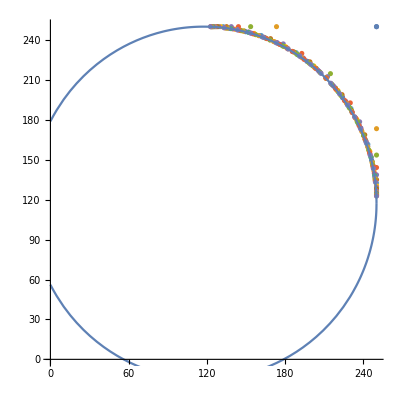

```mathematica
Show[ListPlot[posts,AspectRatio->Automatic,AxesOrigin->{0,0}],Plot[q/.Solve[(p-(√π r)/(2+√π))^2+(q-(√π r)/(2+√π))^2==((2 r)/(2+√π))^2,q],{p,0,r}]]
```

```mathematica
{a,o}={(√π r)/(2+√π),(2 r)/(2+√π)};
tolerance=4/10;
posts={p,q}/.Solve[{(o-tolerance)^2<(p-a)^2+(q-a)^2<(o+tolerance/4)^2,a-1≤p≤q≤r},{p,q},Integers]
```

{{117,250},{118,250},{119,250},{120,250},{121,250},{122,250},{131,249},{132,249},{133,249},{134,249},{138,248},{139,248},{140,248},{144,247},{145,247},{149,246},{150,246},{153,245},{156,244},{157,244},{159,243},{160,243},{162,242},{163,242},{165,241},{167,240},{168,240},{170,239},{172,238},{174,237},{176,236},{178,235},{180,234},{182,233},{184,232},{186,231},{187,230},{189,229},{190,228},{192,227},{193,226},{195,225},{196,224},{197,223},{199,222},{200,221},{201,220},{205,217},{206,216},{207,215},{208,214},{209,213},{210,212},{211,211}}

```mathematica
(*不妨认为{211,211}属于最后选取的桩，采用贪心算法*)
(*宽容度参数*)
k=2;
upto=100;
maxpost=16;
ratio[pending_,selected_]:=Module[{convexhull},
convexhull=ConvexHullMesh[Join[selected,{{0,0},{0,r},{211,211},pending}]];Area[convexhull]/(Perimeter[convexhull]-r-Norm[{211,211}])];
possible=List/@MaximalBy[posts,ratio[#,{}]&,k];
Do[nextpossible=Table[MaximalBy[posts,ratio[#,possible⟦i⟧]&,k]⟦1;;k⟧,{i,1,Length[possible]}];
possible=Flatten[Table[Append[possible⟦i⟧,nextpossible⟦i,j⟧],{i,1,Length[possible]},{j,1,k}],1];
possible=MaximalBy[possible,ratio[{0,0},#]&,UpTo[upto]],maxpost];
DecimalForm[Max[ratio[{0,0},#]&/@possible],{+∞,8}]
```

132.52756426

```mathematica
(*已得到最优答案，但该算法的稳健性很差*)
```